## A ‘toy’ 2D Lyapunov exponent calculation

Simple dynamics in polar coordinates, with stable limit cycle when μ>0.

```mathematica
rDot[μ_, r_]=μ*r-r^3;
Print["ṙ=",rDot[μ, r]]
θDot[ω_, ν_, r_]=ω+ν*r^2;
Print["θ̇=",θDot[ω, ν, r]]
```

ṙ=-r^3+r μ

θ̇=r^2 ν+ω

### Differential equations in cartesian coordinates

The transformations were done by hand.

```mathematica
xDot[x_,y_,μ_,ω_,ν_]=μ*x-x*(x^2+y^2)-y*(ω+ν*(x^2+y^2));
Print["ẋ=",xDot[x,y,μ,ω,ν]]
yDot[x_,y_,μ_,ω_,ν_]=μ*y-y*(x^2+y^2)+x*(ω+ν*(x^2+y^2));
Print["ẏ=",yDot[x,y,μ,ω,ν]]
```

ẋ=-x (x^2+y^2)+x μ-y ((x^2+y^2) ν+ω)

ẏ=-y (x^2+y^2)+y μ+x ((x^2+y^2) ν+ω)

### Stream plot and limit cycle

The limit cycle will be located where rDot = 0. Solving that gives us:

```mathematica
sols=Solve[rDot[μ,r]==0,r]
rCyclePos[μ_]=r/.sols[[3]];
```

{{r→0},{r→-√μ},{r→√μ}}

Since r can not be negative, and r=0 is a fixed point, the limit cycle will be at the square root of μ.
Then we can plug that initial value in the trajectory and superimpose the stream plot to get a visualization of the dynamics.

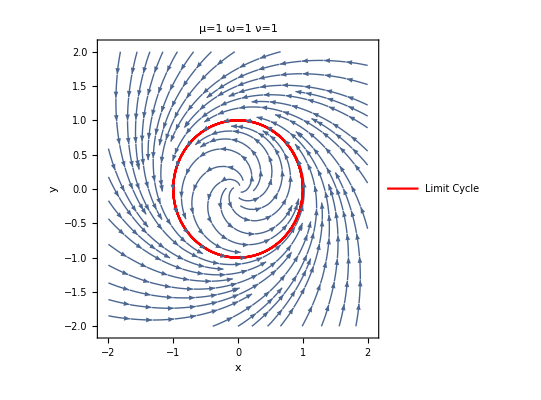

```mathematica
mu=1;
omega= 1;
nu=1;
xDot[x_,y_]=xDot[x,y,mu,omega,nu];
yDot[x_,y_]=yDot[x,y,mu,omega,nu];
tMax=10;
traj[t_,x0_,y0_] := {x[t],y[t]} /. NDSolve[{x'[t]==xDot[x[t],y[t]],y'[t]==yDot[x[t],y[t]],x[0]==x0,y[0]==y0},{x,y},{t,0,tMax}][[1]];
zeroTraj[t_]= traj[t,Sqrt[mu], 0];
zeroTrajPlot=ParametricPlot[zeroTraj[t], {t,0,tMax},PlotStyle->Red,PlotLegends->{"Limit Cycle"}];
streamPlot=StreamPlot[{xDot[x,y],yDot[x,y]},{x,-2,2},{y,-2,2},StreamScale->Automatic,PlotLabel->StringForm["μ=``\tω=``\tν=``",mu,omega,nu],AxesLabel->{"x","y"}];
Show[streamPlot, zeroTrajPlot]
```

### Lyapunov Matrix

It is evident that the new equations are a special case of the general system we are studying with the parameters: μ=1/10, ω=1, and ν=1.

```mathematica
mu=1/10;
omega= 1;
nu=1;
X1Dot[X1_,X2_]=xDot[X1,X2,mu,omega,nu] // Expand ;
X2Dot[X1_,X2_]=yDot[X1,X2,mu,omega,nu] // Expand;
Print["OverDot[X1]=", X1Dot[X1,X2]]
Print["OverDot[X2]=", X2Dot[X1,X2]]
```

OverDot[X1]=X1/10-X1^3-X2-X1^2 X2-X1 X2^2-X2^3

OverDot[X2]=X1+X1^3+X2/10-X1^2 X2+X1 X2^2-X2^3

Knowing this, we can calculate the Jacobian and use NDSolve for the six ordinary differential equations and three initial conditions. The initial conditions are: M[0] = I (identity matrix), X1[0] = Sqrt[μ], X2[0] = 0. The last two initial conditions are used to be positioned on the limit cycle.  The Jacobian is:

```mathematica
M=.;sols=.;jacobian=.;X1=.;X2=.;
X10=Sqrt[mu];
X20=0;
jacobian[X1_,X2_]={{D[X1Dot[X1,X2],X1],D[X1Dot[X1,X2],X2]},{D[X2Dot[X1,X2],X1],D[X2Dot[X1,X2],X2]}};
Print["J=",jacobian[X1,X2]//MatrixForm]
sols=NDSolve[{M'[t]==jacobian[X1[t],X2[t]].M[t],X1'[t]==X1Dot[X1[t],X2[t]], X2'[t]==X2Dot[X1[t],X2[t]],M[0]==IdentityMatrix[2],X1[0]==X10,X2[0]==X20},{X1[t],X2[t],M[t]},{t,0,10}];
X1Sol[t_]=(X1[t]/.sols)[[1]];
X2Sol[t_]=(X2[t]/.sols)[[1]];
MSol[t_]=(M[t]/.sols)[[1]];
```

J=(1/10-3 X1^2-2 X1 X2-X2^2 | -1-X1^2-2 X1 X2-3 X2^2
1+3 X1^2-2 X1 X2+X2^2 | 1/10-X1^2+2 X1 X2-3 X2^2)

### Stable limit cycle and evaluation

The period time can be calculated analytically using the fact that the angle after one period is 2π. First we compute an expression for theta:

```mathematica
θFunc[t_]=(θ[t] /.DSolve[θ'[t]== θDot[ω,ν,Sqrt[μ]], θ[t],t])[[1]];
Print["θ(t)=",θFunc[t]/.C[1]->C]
```

θ(t)=C+t μ ν+t ω

The period time can then be computed by solving  θ(T)-θ(0) =2π:

```mathematica
periodTime[μ_,ω_,ν_]=(t/.Solve[2π-0==θFunc[t]-θFunc[0],t])[[1]];
periodT=periodTime[mu,omega,nu];
Print["T=",periodTime[μ,ω,ν]]
```

T=(2 π)/(μ ν+ω)

Then we can input the period time in the Lyupunov matrix function to get a numerical approximation:

```mathematica
Print["M(0)=",MSol[0] // MatrixForm]
Print["M(T)=",MSol[periodT] // MatrixForm]
```

M(0)=(1. | 0.
0. | 1.)

M(T)=(0.319053 | 1.62572×10^-8
0.680946 | 0.999999)

Finally, we can make a trajectory plot to confirm that our period time is correct.

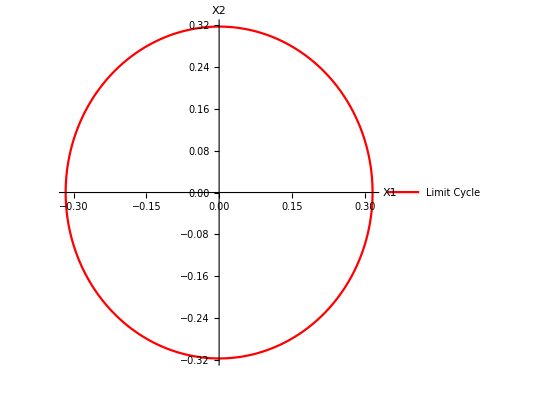

```mathematica
ParametricPlot[{X1Sol[t], X2Sol[t]}, {t,0,periodT},PlotStyle->Red,AxesLabel->{"X1","X2"},PlotLegends->{"Limit Cycle"}]
```

To avoid the fact that our period time is an over estimate, we can calculate the positional difference between time 0 and our period time. The distance between the points for t=0 and t=T is:

```mathematica
Norm[{X1Sol[0],X2Sol[0]}-{X1Sol[periodT],X2Sol[periodT]}]
```

2.02611×10^-7

This difference is small enough to be considered negligible.

### Analytical analysis of Lyapunov Matrix

We solved the lyupunov matrix for polar coordinates using the jacobian in polar coordinates and and r=r_C. We also use the fact that M[0] = I (identity matrix). 

First, calculate the jacobian in polar coordinates.

```mathematica
jacobian[r_,θ_,μ_,ω_,ν_]={{D[rDot[μ,r],r],D[rDot[μ,r],θ]},{D[θDot[ω, ν, r],r],D[θDot[ω, ν, r],θ]}};
Print["J(r,θ)=",jacobian[r,θ,μ,ω,ν]//MatrixForm]
```

J(r,θ)=(-3 r^2+μ | 0
2 r ν | 0)

Then we will use the jacobian on the limit cycle.

```mathematica
jacobianOnLimit[μ_,ω_,ν_]=jacobian[Sqrt[μ],θ, μ,ω,ν];
Print["J(√μ, 0)=",jacobianOnLimit[μ,ω,ν]//MatrixForm]
```

J(√μ, 0)=(-2 μ | 0
2 √μ ν | 0)

Calculate the lyupunov matrix analytically using the fact that the jacobian is a constant on the limit cycle (then we can easily solve the differential equation).

```mathematica
lyupunovMatrix[μ_,ω_,ν_]=MatrixExp[jacobianOnLimit[μ,ω,ν]*t].IdentityMatrix[2];
Print["M(t)=", lyupunovMatrix[μ,ω,ν]//Simplify//MatrixForm]
```

M(t)=(ⅇ^(-2 t μ) | 0
(ⅇ^(-2 t μ) (-1+ⅇ^(2 t μ)) ν)/(√μ) | 1)

Then we want to compare our numerical and analytical solution for the lyupunov matrix. 

First we have to transform our analytical lyupunov matrix from polar to cartesian coordinates. The (very messy) result is:

```mathematica
r[x_,y_]=Sqrt[x^2+y^2];
θ[x_,y_]=ArcTan[y/x];
jacobianTrans={{D[r[x,y],x],D[r[x,y],y]},{D[θ[x,y],x],D[θ[x,y],y]}};
analyticalLyupunov[t_,x_,y_,μ_,ω_,ν_]=Inverse[jacobianTrans] . lyupunovMatrix[μ,ω,ν] .jacobianTrans //Simplify;
Print["M(x,y,t)=",analyticalLyupunov[t,x,y,μ,ω,ν]//FullSimplify//MatrixForm]
analyticalLyupunovAtPeriodT=analyticalLyupunov[periodT,Sqrt[mu],0,mu,omega,nu];
```

M(x,y,t)=((ⅇ^(-2 t μ) (x^2 √μ+ⅇ^(2 t μ) y^2 √μ-(-1+ⅇ^(2 t μ)) x y √(x^2+y^2) ν))/((x^2+y^2) √μ) | ((-1+ⅇ^(-2 t μ)) y (x √(x^2+y^2) √μ+x^2 y ν+y^3 ν))/((x^2+y^2)^(3/2) √μ)
(ⅇ^(-2 t μ) (-1+ⅇ^(2 t μ)) x (-y √(x^2+y^2) √μ+x^3 ν+x y^2 ν))/((x^2+y^2)^(3/2) √μ) | (x^2+ⅇ^(-2 t μ) y^2+(ⅇ^(-2 t μ) (-1+ⅇ^(2 t μ)) x y √(x^2+y^2) ν)/(√μ))/(x^2+y^2))

Finally we will compare our numerical and analytical results for the lyupunov matrix. We will compare both the matrices and their eigenvalues.

```mathematica
Print["M_numeric(T)=",MSol[periodT] // MatrixForm]
Print["M_analytic(T)=",analyticalLyupunovAtPeriodT//MatrixForm//N]
```

M_numeric(T)=(0.319053 | 1.62572×10^-8
0.680946 | 0.999999)

M_analytic(T)=(0.319053 | 0.
0.680947 | 1.)

The matrices are very similar and the eigenvalues for the numerical and analytical respectively are also almost identical:

```mathematica
Eigenvalues[MSol[periodT]]//MatrixForm
Eigenvalues[analyticalLyupunovAtPeriodT]//N//MatrixForm
```

(0.999999
0.319053)

(1.
0.319053)

With this comparison we can see that our analytical and numerical calculations give the same results.

## Lyapunov exponents for the Lorenz equations

First we will define three lorenz equations for this 3-dimensional dynamical system.

```mathematica
xDot[σ_,x_,y_,z_]=σ*(y-x);
yDot[r_,x_,y_,z_]=r*x-y-x*z;
zDot[b_,x_,y_,z_]=x*y-b*z;
σValue=10;
bValue=8/3;
rValue=28;
Print["ẋ=",xDot[σ,x,y,z]]
Print["ẏ=",yDot[r,x,y,z]]
Print["ż=",zDot[b,x,y,z]]
Print["σ=10, b=8/3, r=28"]
```

ẋ=(-x+y) σ

ẏ=r x-y-x z

ż=x y-b z

σ=10, b=8/3, r=28

We will also compute the Jacobian.

```mathematica
jacobian[σ_,r_,b_,x_,y_,z_]={{D[xDot[σ,x,y,z],x],D[xDot[σ,x,y,z],y],D[xDot[σ,x,y,z],z]},{D[yDot[r,x,y,z],x],D[yDot[r,x,y,z],y],D[yDot[r,x,y,z],z]},{D[zDot[b,x,y,z],x],D[zDot[b,x,y,z],y],D[zDot[b,x,y,z],z]}};
Print["J(x,y,z)=",jacobian[σ,r,b,x,y,z]//MatrixForm]
```

J(x,y,z)=(-σ | σ | 0
r-z | -1 | -x
y | x | -b)

### Solve equations and plot attractor

We can also analyze the eigenvalues of the jacobian around origin to see its stability.

```mathematica
jaccy=jacobian[σValue,rValue,bValue,0,0,0];
Print["J(0,0,0)=",jaccy//MatrixForm]
Print["eig(J)=",Eigenvalues[jaccy]//N//MatrixForm]
```

J(0,0,0)=(-10 | 10 | 0
28 | -1 | 0
0 | 0 | -8/3)

eig(J)=(-22.8277
11.8277
-2.66667)

Since one eigenvalue is positive (and the other two negative), the origin is a saddle point, and we can use that as an initial position (with small deviation to not be stationary).

First we will solve the equations using NDSolve for a point very close to the origin (the deviation is 10^-2).

```mathematica
t=.;
deviation=10^(-2);
sols=NDSolve[{x'[t]==xDot[σValue,x[t],y[t],z[t]], y'[t]==yDot[rValue,x[t],y[t],z[t]],z'[t]==zDot[bValue,x[t],y[t],z[t]],x[0]==deviation,y[0]==deviation,z[0]==deviation},{x[t],y[t],z[t]}, {t,0,10^3.5}];
xSol[t_]=(x[t]/.sols)[[1]];
ySol[t_]=(y[t]/.sols)[[1]];
zSol[t_]=(z[t]/.sols)[[1]];
```

The solutions for the trajectories can then be plotted to visualize the strange attractor. We will neglect the first ~100 time steps, since our initial condition is not part of the attractor.

```mathematica
ParametricPlot3D[{xSol[t], ySol[t], zSol[t]}, {t,10^2,1.5*10^2},PlotStyle->Red,AxesLabel->{"x","y","z"}, PlotLegends->{"Lorenz Attractor"}]
```

-Graphics3D-

### Prove λ_1+λ_2+λ_3=tr(J)=-b-1-σ analytically

The change in volume can be described as V̇=∫_V dV*tr(J). 

tr(J) for our Lorenz system of equations is equal to -b-1-σ (constant), as can be seen below.

```mathematica
Print["Tr(J)=",Tr[jacobian[σ,r,b,x,y,z]]]
```

Tr(J)=-1-b-σ

This can be further simplified to V̇=V*tr(J) if the dissipation rate tr(J) is constant (as in our case). Thus giving us V=V_0*e^(tr(J)*t). 

We also have V~V_0*det(M)=V_0*m_1*m_2*m_3~V_0*e^((λ_1+λ_2+λ_3)*t). If we put this equation equal to the one above we find that V_0*e^((λ_1+λ_2+λ_3)*t)=V_0*e^(tr(J)*t), thus (λ_1+λ_2+λ_3)=tr(J).

### Compute Lyapunov exponents for the Lorenz attractor

Following the lecture notes, we implemented an algorithm for numerically calculating the lyapunov exponents. After some experimenting, a delta time value of 10^-4 was chosen, together with 1 000 000 iterations.

```mathematica
deltaT=10^(-4);
nIterations=10^6;
lambdas = {0,0,0};
time=6*10^2;
Q=IdentityMatrix[3];
Do[(M= IdentityMatrix[3] + jacobian[σValue,rValue,bValue,xSol[time],ySol[time],zSol[time]]*deltaT;{Qnew,Rnew} = QRDecomposition[M.Q]; Q=Transpose[Qnew];lambdas+=Log[Abs[Diagonal[Rnew]]]/(nIterations*deltaT);time+=deltaT;),{i,nIterations}];
Print["λ=",lambdas//MatrixForm]
Print["λ_1+λ_2+λ_3=",Total[lambdas]]
Print["-b-1-σ=",-bValue-1-σValue//N]
```

λ=(0.887564
-0.0129403
-14.5448)

λ_1+λ_2+λ_3=-13.6701

-b-1-σ=-13.6667

As we can see by the results, the sum of the Lyapunov exponents are very close to the trace of the jacobian, and the individual values are also very close to the values from the exercise sheet.

### Compute exponents for other parameters (σ, b, r)

Now we will apply the same algorithm from the previous task, with new parameters: σ=16, b=4, and r=46.

```mathematica
σValue=16;bValue=4;rValue=46;
sols=NDSolve[{x'[t]==xDot[σValue,x[t],y[t],z[t]], y'[t]==yDot[rValue,x[t],y[t],z[t]],z'[t]==zDot[bValue,x[t],y[t],z[t]],x[0]==deviation,y[0]==deviation,z[0]==deviation},{x[t],y[t],z[t]}, {t,0,10^3.5}];
xSol[t_]=(x[t]/.sols)[[1]];
ySol[t_]=(y[t]/.sols)[[1]];
zSol[t_]=(z[t]/.sols)[[1]];
```

```mathematica
deltaT=10^(-4);
nIterations=10^6;
lambdas = {0,0,0};
time=6*10^2;
Q=IdentityMatrix[3];
Do[(M= IdentityMatrix[3] + jacobian[σValue,rValue,bValue,xSol[time],ySol[time],zSol[time]]*deltaT;{Qnew,Rnew} = QRDecomposition[M.Q]; Q=Transpose[Qnew];lambdas+=Log[Abs[Diagonal[Rnew]]]/(nIterations*deltaT);time+=deltaT;),{i,nIterations}];
Print["λ=",lambdas//MatrixForm]
Print["λ_1+λ_2+λ_3=",Total[lambdas]]
Print["-b-1-σ=",-bValue-1-σValue//N]
```

λ=(1.52476
-0.0191612
-22.5124)

λ_1+λ_2+λ_3=-21.0068

-b-1-σ=-21.

In this task, we are also close with the sum of the exponents.